```mathematica
Clear[e]
Clear[b]
Clear[w]
Clear[c]
Clear[a]
```

```mathematica
p=((-1+e) (-b+c-b e w+a c e w+a b e^2 w-a c e^2 w+b w^2-a b w^2-c w^2+a c w^2-3 b e w^2+3 a b e w^2+a^2 b e w^2+2 c e w^2-3 a c e w^2-a^2 c e w^2+2 b e^2 w^2-2 a b e^2 w^2+a^2 b e^2 w^2-c e^2 w^2+3 a c e^2 w^2+a^2 c e^2 w^2-a^2 b e^3 w^2-a c e^3 w^2+a^2 b w^3-a^2 c w^3-a b e w^3-a^2 b e w^3-a c e w^3+4 a^2 c e w^3+3 a b e^2 w^3-2 a^2 b e^2 w^3+2 a c e^2 w^3-5 a^2 c e^2 w^3-2 a b e^3 w^3+2 a^2 b e^3 w^3-a c e^3 w^3+2 a^2 c e^3 w^3))/((-1+w) (-1-e w-a e w+a e^2 w+w^2-a w^2-3 e w^2+2 a e w^2+a^2 e w^2+2 e^2 w^2-a e^2 w^2-a^2 e^2 w^2+a^2 w^3-4 a^2 e w^3+6 a^2 e^2 w^3-4 a^2 e^3 w^3+a^2 e^4 w^3))
```

((-1+e) (-b+c-b e w+a c e w+a b e^2 w-a c e^2 w+b w^2-a b w^2-c w^2+a c w^2-3 b e w^2+3 a b e w^2+a^2 b e w^2+2 c e w^2-3 a c e w^2-a^2 c e w^2+2 b e^2 w^2-2 a b e^2 w^2+a^2 b e^2 w^2-c e^2 w^2+3 a c e^2 w^2+a^2 c e^2 w^2-a^2 b e^3 w^2-a c e^3 w^2+a^2 b w^3-a^2 c w^3-a b e w^3-a^2 b e w^3-a c e w^3+4 a^2 c e w^3+3 a b e^2 w^3-2 a^2 b e^2 w^3+2 a c e^2 w^3-5 a^2 c e^2 w^3-2 a b e^3 w^3+2 a^2 b e^3 w^3-a c e^3 w^3+2 a^2 c e^3 w^3))/((-1+w) (-1-e w-a e w+a e^2 w+w^2-a w^2-3 e w^2+2 a e w^2+a^2 e w^2+2 e^2 w^2-a e^2 w^2-a^2 e^2 w^2+a^2 w^3-4 a^2 e w^3+6 a^2 e^2 w^3-4 a^2 e^3 w^3+a^2 e^4 w^3))

```mathematica
v = -((b-c-b e+c e+b e w-2 a b e w-c e w+2 a c e w-2 b e^2 w+3 a b e^2 w-a^2 b e^2 w+2 c e^2 w-3 a c e^2 w+a^2 c e^2 w+b e^3 w-a b e^3 w+a^2 b e^3 w-c e^3 w+a c e^3 w-a^2 c e^3 w-b e^3 w^2+3 a b e^3 w^2-3 a^2 b e^3 w^2+2 a^3 b e^3 w^2+c e^3 w^2-3 a c e^3 w^2+3 a^2 c e^3 w^2-2 a^3 c e^3 w^2+b e^4 w^2-3 a b e^4 w^2+3 a^2 b e^4 w^2-2 a^3 b e^4 w^2-c e^4 w^2+3 a c e^4 w^2-3 a^2 c e^4 w^2+2 a^3 c e^4 w^2)/((-1+w) (1+2 e w-2 a e w-2 e^2 w+2 a e^2 w-2 a^2 e^2 w+e^2 w^2-2 a e^2 w^2-2 e^3 w^2+6 a e^3 w^2-6 a^2 e^3 w^2+4 a^3 e^3 w^2)))
```

-((b-c-b e+c e+b e w-2 a b e w-c e w+2 a c e w-2 b e^2 w+3 a b e^2 w-a^2 b e^2 w+2 c e^2 w-3 a c e^2 w+a^2 c e^2 w+b e^3 w-a b e^3 w+a^2 b e^3 w-c e^3 w+a c e^3 w-a^2 c e^3 w-b e^3 w^2+3 a b e^3 w^2-3 a^2 b e^3 w^2+2 a^3 b e^3 w^2+c e^3 w^2-3 a c e^3 w^2+3 a^2 c e^3 w^2-2 a^3 c e^3 w^2+b e^4 w^2-3 a b e^4 w^2+3 a^2 b e^4 w^2-2 a^3 b e^4 w^2-c e^4 w^2+3 a c e^4 w^2-3 a^2 c e^4 w^2+2 a^3 c e^4 w^2)/((-1+w) (1+2 e w-2 a e w-2 e^2 w+2 a e^2 w-2 a^2 e^2 w+e^2 w^2-2 a e^2 w^2-2 e^3 w^2+6 a e^3 w^2-6 a^2 e^3 w^2+4 a^3 e^3 w^2)))

```mathematica
pdiff = v - p
```

-((b-c-b e+c e+b e w-2 a b e w-c e w+2 a c e w-2 b e^2 w+3 a b e^2 w-a^2 b e^2 w+2 c e^2 w-3 a c e^2 w+a^2 c e^2 w+b e^3 w-a b e^3 w+a^2 b e^3 w-c e^3 w+a c e^3 w-a^2 c e^3 w-b e^3 w^2+3 a b e^3 w^2-3 a^2 b e^3 w^2+2 a^3 b e^3 w^2+c e^3 w^2-3 a c e^3 w^2+3 a^2 c e^3 w^2-2 a^3 c e^3 w^2+b e^4 w^2-3 a b e^4 w^2+3 a^2 b e^4 w^2-2 a^3 b e^4 w^2-c e^4 w^2+3 a c e^4 w^2-3 a^2 c e^4 w^2+2 a^3 c e^4 w^2)/((-1+w) (1+2 e w-2 a e w-2 e^2 w+2 a e^2 w-2 a^2 e^2 w+e^2 w^2-2 a e^2 w^2-2 e^3 w^2+6 a e^3 w^2-6 a^2 e^3 w^2+4 a^3 e^3 w^2)))-((-1+e) (-b+c-b e w+a c e w+a b e^2 w-a c e^2 w+b w^2-a b w^2-c w^2+a c w^2-3 b e w^2+3 a b e w^2+a^2 b e w^2+2 c e w^2-3 a c e w^2-a^2 c e w^2+2 b e^2 w^2-2 a b e^2 w^2+a^2 b e^2 w^2-c e^2 w^2+3 a c e^2 w^2+a^2 c e^2 w^2-a^2 b e^3 w^2-a c e^3 w^2+a^2 b w^3-a^2 c w^3-a b e w^3-a^2 b e w^3-a c e w^3+4 a^2 c e w^3+3 a b e^2 w^3-2 a^2 b e^2 w^3+2 a c e^2 w^3-5 a^2 c e^2 w^3-2 a b e^3 w^3+2 a^2 b e^3 w^3-a c e^3 w^3+2 a^2 c e^3 w^3))/((-1+w) (-1-e w-a e w+a e^2 w+w^2-a w^2-3 e w^2+2 a e w^2+a^2 e w^2+2 e^2 w^2-a e^2 w^2-a^2 e^2 w^2+a^2 w^3-4 a^2 e w^3+6 a^2 e^2 w^3-4 a^2 e^3 w^3+a^2 e^4 w^3))

```mathematica
pdiff1 = pdiff/.{b->3, c->1, w->.98,  e->.01}
```

-(49.5 (-0.175348-1.89009 a+1.91036 a^2))/(-0.0780199-0.95099 a+0.913613 a^2)+(50. (1.99921-0.0386083 a-0.000199745 a^2+3.80318×10^-6 a^3))/(1.0195-0.0195903 a-0.000201762 a^2+3.8416×10^-6 a^3)

```mathematica
pdiff2 = pdiff/.{b->3, c->1, w->.98,  e->.1}
```

-(45. (-0.99746-1.53627 a+2.10812 a^2))/(-0.406512-0.866124 a+0.703952 a^2)+(50. (1.95703-0.329974 a-0.0228262 a^2+0.00345744 a^3))/(1.18408-0.189846 a-0.0253624 a^2+0.0038416 a^3)

```mathematica
pdiff3 = pdiff/.{b->3, c->1, w->.98,  e->.3}
```

-(35. (-2.54586-0.382454 a+2.28045 a^2))/(-1.02509-0.676396 a+0.427664 a^2)+(50. (1.65182-0.590811 a-0.232389 a^2+0.0726062 a^3))/(1.44617-0.428887 a-0.331985 a^2+0.103723 a^3)

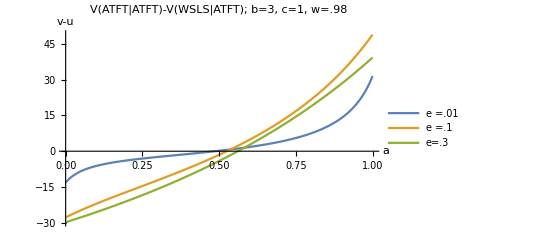

```mathematica
Plot[{pdiff1, pdiff2, pdiff3}, {a, 0, 1}, PlotLegends->Placed[LineLegend[{"e =.01","e =.1","e=.3"}],{0.3, 0.7}],AxesLabel->{"a","v-u"},PlotLabel->"V(ATFT|ATFT)-V(WSLS|ATFT); b=3, c=1, w=.98"]
```